```mathematica
Clear[k,g1,g2,Γ,γw
];
kB=1.38*10^-23;T=273+36;c=3*10^8;d=2.537 10^(-29);h=2 Pi 1.0545718 10^-34;ep0=8.854 10^-12;
mass=87*1.6*10^-27;
Γ=6 10^6;
MB[velocity_]:=Evaluate[Sqrt[mass/(2 Pi kB T)] Exp[-mass velocity^2/(2 kB T)]];

dia=0.2;area=Pi dia^2/4;
Pc=3.5;Pp=0.3;
Ic=Pc/area;Ip=Pp/area;
Isat=2.5;
Rc=Γ Sqrt[Ic/2/Isat];
Rp=Γ Sqrt[Ip/2/Isat];
caj=√(5/4); 
cal=√(1/4);
can=√(1/24);
cai=-√(5/24);
cam=-√(1/8);
cbi=-√(5/24);
cbk=√(5/24);
cbm=√(1/8);
cbo=√(1/8);
cbj=0;
cbn=-√(1/6);
ccj=-√(5/24);
 ccn=√(1/24);
ccp=√(1/4);
cck=√(5/24) ;
cco=- √(1/8) ;
 cdi=√(1/20) ;
cdm=√(1/12) ;
cdl= -√(1/6);
cel=- √(1/12) ;
cej=√(1/40) ;
cei=√(1/40) ;
cen=√(1/8) ;
cem= - √(1/24) ;
cfi=√(1/120);
cfk=√(1/120);
cfm=-√(1/8);
cfo=√(1/8);
cfj=√(1/30);
cfn=0;
cgj=√(1/40);
cgn=-√(1/8);
cgp=√(1/12);
cgk=√(1/40);
cgo=√(1/24);
chk=√(1/20);
cho=-√(1/12);
chp=√(1/6);
g1=0.70*10^6;
g2=0.93*10^6;
B=0;
γb=0.2 10^6;
γd=1/625 γb;
γw=1000;
k=1/780*10^9;
Δe=157*10^6;
δp=0;
δc=0;
Rpl= Rp Abs@Sin[theta-Pi/4];
Rph= Rp Abs@Cos[theta-Pi/4];
Rcl= Rc Abs@Cos[theta-Pi/4];
Rch= Rc Abs@Sin[theta-Pi/4];
theta=Pi/180*0;
v=0;

r={{raa[t],rab[t],rac[t],rad[t],rae[t],raf[t],rag[t],rah[t],rai[t],raj[t],rak[t],ral[t],ram[t],ran[t],rao[t],rap[t]},{rba[t],rbb[t],rbc[t],rbd[t],rbe[t],rbf[t],rbg[t],rbh[t],rbi[t],rbj[t],rbk[t],rbl[t],rbm[t],rbn[t],rbo[t],rbp[t]},{rca[t],rcb[t],rcc[t],rcd[t],rce[t],rcf[t],rcg[t],rch[t],rci[t],rcj[t],rck[t],rcl[t],rcm[t],rcn[t],rco[t],rcp[t]},{rda[t],rdb[t],rdc[t],rdd[t],rde[t],rdf[t],rdg[t],rdh[t],rdi[t],rdj[t],rdk[t],rdl[t],rdm[t],rdn[t],rdo[t],rdp[t]},{rea[t],reb[t],rec[t],red[t],ree[t],ref[t],reg[t],reh[t],rei[t],rej[t],rek[t],rel[t],rem[t],ren[t],reo[t],rep[t]},{rfa[t],rfb[t],rfc[t],rfd[t],rfe[t],rff[t],rfg[t],rfh[t],rfi[t],rfj[t],rfk[t],rfl[t],rfm[t],rfn[t],rfo[t],rfp[t]},{rga[t],rgb[t],rgc[t],rgd[t],rge[t],rgf[t],rgg[t],rgh[t],rgi[t],rgj[t],rgk[t],rgl[t],rgm[t],rgn[t],rgo[t],rgp[t]},{rha[t],rhb[t],rhc[t],rhd[t],rhe[t],rhf[t],rhg[t],rhh[t],rhi[t],rhj[t],rhk[t],rhl[t],rhm[t],rhn[t],rho[t],rhp[t]},{ria[t],rib[t],ric[t],rid[t],rie[t],rif[t],rig[t],rih[t],rii[t],rij[t],rik[t],ril[t],rim[t],rin[t],rio[t],rip[t]},{rja[t],rjb[t],rjc[t],rjd[t],rje[t],rjf[t],rjg[t],rjh[t],rji[t],rjj[t],rjk[t],rjl[t],rjm[t],rjn[t],rjo[t],rjp[t]},{rka[t],rkb[t],rkc[t],rkd[t],rke[t],rkf[t],rkg[t],rkh[t],rki[t],rkj[t],rkk[t],rkl[t],rkm[t],rkn[t],rko[t],rkp[t]},{rla[t],rlb[t],rlc[t],rld[t],rle[t],rlf[t],rlg[t],rlh[t],rli[t],rlj[t],rlk[t],rll[t],rlm[t],rln[t],rlo[t],rlp[t]},{rma[t],rmb[t],rmc[t],rmd[t],rme[t],rmf[t],rmg[t],rmh[t],rmi[t],rmj[t],rmk[t],rml[t],rmm[t],rmn[t],rmo[t],rmp[t]},{rna[t],rnb[t],rnc[t],rnd[t],rne[t],rnf[t],rng[t],rnh[t],rni[t],rnj[t],rnk[t],rnl[t],rnm[t],rnn[t],rno[t],rnp[t]},{roa[t],rob[t],roc[t],rod[t],roe[t],rof[t],rog[t],roh[t],roi[t],roj[t],rok[t],rol[t],rom[t],ron[t],roo[t],rop[t]},{rpa[t],rpb[t],rpc[t],rpd[t],rpe[t],rpf[t],rpg[t],rph[t],rpi[t],rpj[t],rpk[t],rpl[t],rpm[t],rpn[t],rpo[t],rpp[t]}};
hi= {{0,0,0,0,0,0,0,0,0,- caj Rph/2,0,- cal Rpl/2,0,- can Rph/2,0,0},{0,0,0,0,0,0,0,0,- cbi Rpl/2,0,- cbk Rph/2,0,- cbm Rpl/2,0,- cbo Rph/2,0},{0,0,0,0,0,0,0,0,0,- ccj Rpl/2,0,0,0,- ccn Rpl/2,0,- ccp Rph/2},{0,0,0,0,0,0,0,0,- cdi Rch/2,0,0,0,- cdm Rch/2,0,0,0},{0,0,0,0,0,0,0,0,0,- cej Rch/2,0,- cel Rcl/2,0,- cen Rch/2,0,0},{0,0,0,0,0,0,0,0,- cfi Rcl/2,0,- cfk Rch/2,0,- cfm Rcl/2,0,- cfo Rch/2,0},{0,0,0,0,0,0,0,0,0,- cgj Rcl/2,0,0,0,- cgn Rcl/2,0,- cgp Rch/2},{0,0,0,0,0,0,0,0,0,0,- chk Rcl/2,0,0,0,- cho Rcl/2,0},{0,- cbi Rpl/2,0,- cdi Rch/2,0,- cfi Rcl/2,0,0,0,0,0,0,0,0,0,0},{- caj Rph/2,0,- ccj Rpl/2,0,- cej Rch/2,0,- cgj Rcl/2,0,0,0,0,0,0,0,0,0},{0,- cbk Rph/2,0,0,0,- cfk Rch/2,0,- chk Rcl/2,0,0,0,0,0,0,0,0},{- cal Rpl/2,0,0,0,- cel Rcl/2,0,0,0,0,0,0,0,0,0,0,0},{0,- cbm Rpl/2,0,- cdm Rch/2,0,- cfm Rcl/2,0,0,0,0,0,0,0,0,0,0},{- can Rph/2,0,- ccn Rpl/2,0,- cen Rch/2,0,- cgn Rcl/2,0,0,0,0,0,0,0,0,0},{0,- cbo Rph/2,0,0,0,- cfo Rch/2,0,- cho Rcl/2,0,0,0,0,0,0,0,0},{0,0,- ccp Rph/2,0,0,0,- cgp Rch/2,0,0,0,0,0,0,0,0,0}};
h0={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,δp-δc,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,δp-δc,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,δp-δc,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,δp-δc,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,δp-δc,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,-Δe+δp-k v,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,-Δe+δp-k v,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,-Δe+δp-k v,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,δp-k v,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,δp-k v,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,δp-k v,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,δp-k v,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,δp-k v}};
hb=B {{+ g1 ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,- g1,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,- 2 g1,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,- g1,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,g1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2 g1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,- g2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,g2,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,- 2 g2,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,- g2,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,g2,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 g2}};
h=hi+h0+hb;
de= Γ{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}};
repop=Γ {{1/5 rii[t] +1/6 rjj[t] +1/3 rll[t]+ 1/5 rmm[t]+ 1/6 rnn[t],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,1/5 rii[t]+ 1/6rjj[t] + 1/5 rkk[t]+1/5 rmm[t]+ 1/6 rnn[t] + 1/5 roo[t],0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,1/6 rjj[t] + 1/5 rkk[t] + 1/6 rnn[t]+ 1/5 roo[t] +1/3 rpp[t],0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1/5 rii[t]+ 1/3 rll[t] + 1/5 rmm[t],0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1/5 rii[t] + 1/6 rjj[t] + 1/3 rll[t]+1/5 rmm[t] + 1/6 rnn[t],0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1/5 rii[t]+ 1/6 rjj[t] + 1/5 rkk[t]+ 1/5 rmm[t]+ 1/6 rnn[t] + 1/5 roo[t],0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0, 1/6 rjj[t] + 1/5 rkk[t] + 1/6 rnn[t]+1/5 roo[t]+ 1/3 rpp[t],0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0, 1/5 rkk[t]+ 1/5 roo[t] + 1/3 rpp[t],0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
gde=γw r;
commutator= (h.r - r.h);
anti= (r.de+de.r);
init={raa[0]==1/8,rab[0]==0,rac[0]==0,rad[0]==0,rae[0]==0,raf[0]==0,rag[0]==0,rah[0]==0,rai[0]==0,raj[0]==0,rak[0]==0,ral[0]==0,ram[0]==0,ran[0]==0,rao[0]==0,rap[0]==0,rba[0]==0,rbb[0]==1/8,rbc[0]==0,rbd[0]==0,rbe[0]==0,rbf[0]==0,rbg[0]==0,rbh[0]==0,rbi[0]==0,rbj[0]==0,rbk[0]==0,rbl[0]==0,rbm[0]==0,rbn[0]==0,rbo[0]==0,rbp[0]==0,rca[0]==0,rcb[0]==0,rcc[0]==1/8,rcd[0]==0,rce[0]==0,rcf[0]==0,rcg[0]==0,rch[0]==0,rci[0]==0,rcj[0]==0,rck[0]==0,rcl[0]==0,rcm[0]==0,rcn[0]==0,rco[0]==0,rcp[0]==0,
rda[0]==0,rdb[0]==0,rdc[0]==0,rdd[0]==1/8,rde[0]==0,rdf[0]==0,rdg[0]==0,rdh[0]==0,rdi[0]==0,rdj[0]==0,rdk[0]==0,rdl[0]==0,rdm[0]==0,rdn[0]==0,rdo[0]==0,rdp[0]==0,rea[0]==0,reb[0]==0,rec[0]==0,red[0]==0,ree[0]==1/8,ref[0]==0,reg[0]==0,reh[0]==0,rei[0]==0,rej[0]==0,rek[0]==0,rel[0]==0,rem[0]==0,ren[0]==0,reo[0]==0,rep[0]==0,rfa[0]==0,rfb[0]==0,rfc[0]==0,rfd[0]==0,rfe[0]==0,rff[0]==1/8,rfg[0]==0,rfh[0]==0,rfi[0]==0,rfj[0]==0,rfk[0]==0,rfl[0]==0,rfm[0]==0,rfn[0]==0,rfo[0]==0,rfp[0]==0,rga[0]==0,rgb[0]==0,rgc[0]==0,rgd[0]==0,rge[0]==0,rgf[0]==0,rgg[0]==1/8,rgh[0]==0,rgi[0]==0,rgj[0]==0,rgk[0]==0,rgl[0]==0,rgm[0]==0,rgn[0]==0,rgo[0]==0,rgp[0]==0,
rha[0]==0,rhb[0]==0,rhc[0]==0,rhd[0]==0,rhe[0]==0,rhf[0]==0,rhg[0]==0,rhh[0]==1/8,rhi[0]==0,rhj[0]==0,rhk[0]==0,rhl[0]==0,rhm[0]==0,rhn[0]==0,rho[0]==0,rhp[0]==0,ria[0]==0,rib[0]==0,ric[0]==0,rid[0]==0,rie[0]==0,rif[0]==0,rig[0]==0,rih[0]==0,rii[0]==0,rij[0]==0,rik[0]==0,ril[0]==0,rim[0]==0,rin[0]==0,rio[0]==0,rip[0]==0,rja[0]==0,rjb[0]==0,rjc[0]==0,rjd[0]==0,rje[0]==0,rjf[0]==0,rjg[0]==0,rjh[0]==0,rji[0]==0,rjj[0]==0,rjk[0]==0,rjl[0]==0,rjm[0]==0,rjn[0]==0,rjo[0]==0,rjp[0]==0,rka[0]==0,rkb[0]==0,rkc[0]==0,rkd[0]==0,rke[0]==0,rkf[0]==0,rkg[0]==0,rkh[0]==0,rki[0]==0,rkj[0]==0,rkk[0]==0,rkl[0]==0,rkm[0]==0,rkn[0]==0,rko[0]==0,rkp[0]==0,
rla[0]==0,rlb[0]==0,rlc[0]==0,rld[0]==0,rle[0]==0,rlf[0]==0,rlg[0]==0,rlh[0]==0,rli[0]==0,rlj[0]==0,rlk[0]==0,rll[0]==0,rlm[0]==0,rln[0]==0,rlo[0]==0,rlp[0]==0,rma[0]==0,rmb[0]==0,rmc[0]==0,rmd[0]==0,rme[0]==0,rmf[0]==0,rmg[0]==0,rmh[0]==0,rmi[0]==0,rmj[0]==0,rmk[0]==0,rml[0]==0,rmm[0]==0,rmn[0]==0,rmo[0]==0,rmp[0]==0,rna[0]==0,rnb[0]==0,rnc[0]==0,rnd[0]==0,rne[0]==0,rnf[0]==0,rng[0]==0,rnh[0]==0,rni[0]==0,rnj[0]==0,rnk[0]==0,rnl[0]==0,rnm[0]==0,rnn[0]==0,rno[0]==0,rnp[0]==0,
roa[0]==0,rob[0]==0,roc[0]==0,rod[0]==0,roe[0]==0,rof[0]==0,rog[0]==0,roh[0]==0,roi[0]==0,roj[0]==0,rok[0]==0,rol[0]==0,rom[0]==0,ron[0]==0,roo[0]==0,rop[0]==0,rpa[0]==0,rpb[0]==0,rpc[0]==0,rpd[0]==0,rpe[0]==0,rpf[0]==0,rpg[0]==0,rph[0]==0,rpi[0]==0,rpj[0]==0,rpk[0]==0,rpl[0]==0,rpm[0]==0,rpn[0]==0,rpo[0]==0,rpp[0]==0
};

r1={{raa,rab,rac,rad,rae,raf,rag,rah,rai,raj,rak,ral,ram,ran,rao,rap},{rba,rbb,rbc,rbd,rbe,rbf,rbg,rbh,rbi,rbj,rbk,rbl,rbm,rbn,rbo,rbp},{rca,rcb,rcc,rcd,rce,rcf,rcg,rch,rci,rcj,rck,rcl,rcm,rcn,rco,rcp},{rda,rdb,rdc,rdd,rde,rdf,rdg,rdh,rdi,rdj,rdk,rdl,rdm,rdn,rdo,rdp},{rea,reb,rec,red,ree,ref,reg,reh,rei,rej,rek,rel,rem,ren,reo,rep},{rfa,rfb,rfc,rfd,rfe,rff,rfg,rfh,rfi,rfj,rfk,rfl,rfm,rfn,rfo,rfp},{rga,rgb,rgc,rgd,rge,rgf,rgg,rgh,rgi,rgj,rgk,rgl,rgm,rgn,rgo,rgp},{rha,rhb,rhc,rhd,rhe,rhf,rhg,rhh,rhi,rhj,rhk,rhl,rhm,rhn,rho,rhp},{ria,rib,ric,rid,rie,rif,rig,rih,rii,rij,rik,ril,rim,rin,rio,rip},{rja,rjb,rjc,rjd,rje,rjf,rjg,rjh,rji,rjj,rjk,rjl,rjm,rjn,rjo,rjp},{rka,rkb,rkc,rkd,rke,rkf,rkg,rkh,rki,rkj,rkk,rkl,rkm,rkn,rko,rkp},{rla,rlb,rlc,rld,rle,rlf,rlg,rlh,rli,rlj,rlk,rll,rlm,rln,rlo,rlp},{rma,rmb,rmc,rmd,rme,rmf,rmg,rmh,rmi,rmj,rmk,rml,rmm,rmn,rmo,rmp},{rna,rnb,rnc,rnd,rne,rnf,rng,rnh,rni,rnj,rnk,rnl,rnm,rnn,rno,rnp},{roa,rob,roc,rod,roe,rof,rog,roh,roi,roj,rok,rol,rom,ron,roo,rop},{rpa,rpb,rpc,rpd,rpe,rpf,rpg,rph,rpi,rpj,rpk,rpl,rpm,rpn,rpo,rpp}};
equations=Table[r1[[i,j]]'[t]==-I(commutator[[i,j]])- 1/2 anti[[i,j]]+repop[[i,j]],{i,1,16},{j,1,16}];
```

```mathematica
solution=NDSolve[Flatten[Join[equations,init]],Flatten[r],{t,0,1000*10^-6}];
```

```mathematica
t0=Table[N[t/(6 10^-6)],{t,0,1000*10^-6,10^-7}];
```

```mathematica
f1=Flatten[Table[Re@raa[t]/.solution,{t,0,1000*10^-6,10^-7}]];
f2=Flatten[Table[Re@rbb[t]/.solution,{t,0,1000*10^-6,10^-7}]];
f3=Flatten[Table[Re@rcc[t]/.solution,{t,0,1000*10^-6,10^-7}]];
```

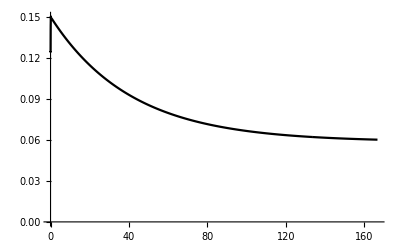

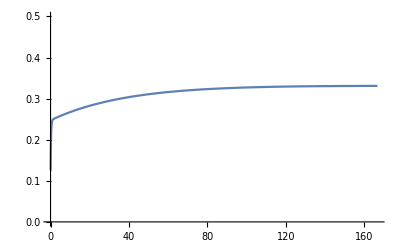

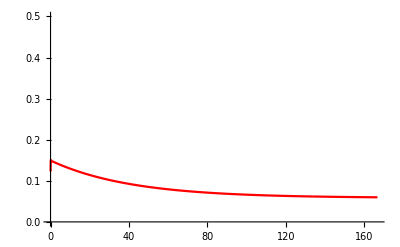

```mathematica
pp1=ListLinePlot[Table[{t0[[i]],f1[[i]]},{i,1,Length[t0]}],PlotRange->All,PlotStyle->Black]
pp2=ListLinePlot[Table[{t0[[i]],f2[[i]]},{i,1,Length[t0]}],PlotRange->{All,{0,0.5}}]
pp3=ListLinePlot[Table[{t0[[i]],f3[[i]]},{i,1,Length[t0]}],PlotRange->{All,{0,0.5}},PlotStyle->Red]
```

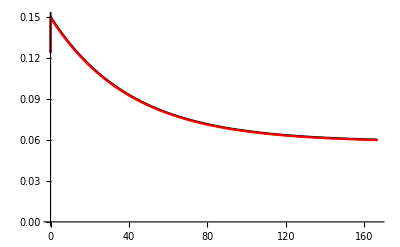

```mathematica
Show[pp1,pp2,pp3]
```

0.999504

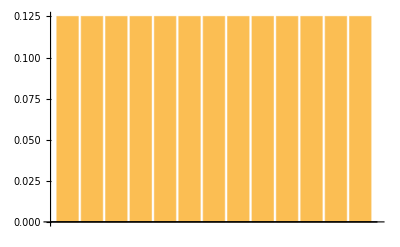

```mathematica
f11=Last[Flatten[Table[Re@raa[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f12=Last[Flatten[Table[Re@rbb[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f13=Last[Flatten[Table[Re@rcc[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f14=Last[Flatten[Table[Re@rdd[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f15=Last[Flatten[Table[Re@ree[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f16=Last[Flatten[Table[Re@rff[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f17=Last[Flatten[Table[Re@rgg[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f18=Last[Flatten[Table[Re@rhh[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f19=Last[Flatten[Table[Re@rii[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f110=Last[Flatten[Table[Re@rjj[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f111=Last[Flatten[Table[Re@rkk[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f112=Last[Flatten[Table[Re@rll[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
f113=Last[Flatten[Table[Re@rmm[t]/.solution,{t,0,1000*10^-6,10^-6}]]];
Total[f11+f12+f13+f14+f15+f16+f17+f18+f19+f110+f111+f112+f113]
data=Table[{i,List[f11,f12,f13,f14,f15,f16,f17,f18,f19,f110,f111,f112,f113][[i]]},{i,1,13}];

BarChart[{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}]
```

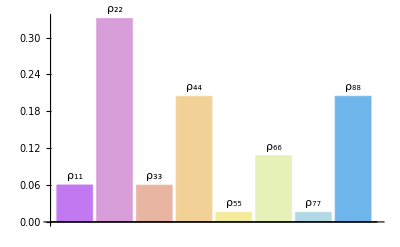

```mathematica
BarChart[List[f11,f12,f13,f14,f15,f16,f17,f18],ChartLabels->Placed[{"ρ_11","ρ_22","ρ_33","ρ_44","ρ_55","ρ_66","ρ_77","ρ_88"},Above],ChartLayout->"Grouped",ChartStyle->"Pastel"]
```